```mathematica
RandomWalkMetropolis[pdf_,start_,times_,proposal_]:=
Module[{f},
	f[current_]:=Module[{w,new},
		new=current+RandomVariate[proposal];
		w=Min[1,pdf[new]/pdf[current]];
		If[RandomReal[]<w,new,current]];
	Return[NestList[f,start,times]];
]
```

```mathematica
pdf[x_]:=1/3*PDF[NormalDistribution[-5,1],x]+2/3*PDF[NormalDistribution[5,1],x];
```

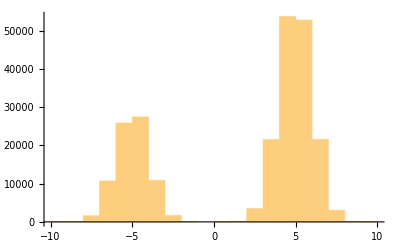

```mathematica
z=RandomWalkMetropolis[pdf,RandomReal[{-10,10}],250000,UniformDistribution[{-10,10}]];
Histogram[z[[15001;;250000]]]
```

```mathematica
z={};
Table[Module[{x},x=RandomWalkMetropolis[pdf,RandomReal[{-10,10}],25000,UniformDistribution[{-10,10}]];z=Join[z,Drop[x,10000]]],{i,1,10}];
```

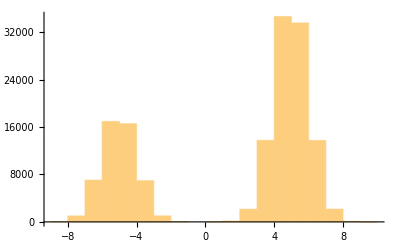

```mathematica
Histogram[z]
```

```mathematica
z={};
Table[Module[{x},x=RandomWalkMetropolis[pdf,RandomReal[{-10,10}],25000,UniformDistribution[{-10,10}]];z=Join[z,Drop[x,10000]]],{i,1,40}];
```

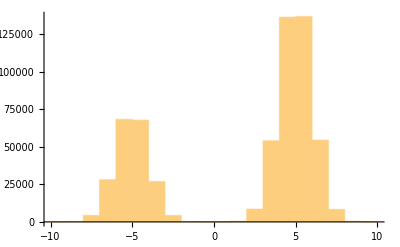

```mathematica
Histogram[z]
```

```mathematica
temperature=1;
DEMC[range_,times_,pdf_]:=
Module[{population,Evolution,size=10,F,final,b=0.000001},
	F=2.4/Sqrt[2*Length[range]];
	population=Table[Map[#[[1]]+RandomReal[#[[2]]-#[[1]]]&,range],{i,size}];
	Evolution[population_]:=
		Module[{CandidateGeneration},
			CandidateGeneration[point_]:=
				Module[{ConstructGeneration,vpoint,selection},
					ConstructGeneration[]:=Module[{potentialpoints},
											potentialpoints=RandomSample[population,2];
											Return[If[MemberQ[potentialpoints,point],ConstructGeneration[],potentialpoints]]];
					vpoint[]:=Module[{points},
						points=ConstructGeneration[];
						Return[point+F*(points[[1]]-points[[2]])+RandomReal[{-b,b},Length[point]]]];
					selection[]:=Module[{upoint},
						upoint=vpoint[];
						Return[If[Log[pdf[upoint]/pdf[point]]>temperature*Log[RandomReal[]],
									upoint,
									point]]];
					Return[selection[]]];					 
			Return[Map[CandidateGeneration,population]]];
	Return[NestList[Evolution,population,times]]];
```

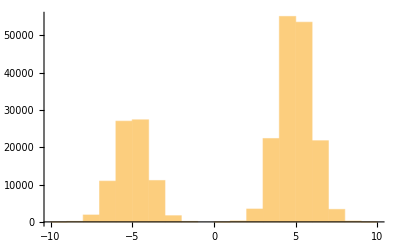

```mathematica
pdf[x_]:=1/3*PDF[NormalDistribution[-5,1],x[[1]]]+2/3*PDF[NormalDistribution[5,1],x[[1]]];
r=DEMC[{{-5,5}},25000,pdf];
track=Table[Map[#[[i,1]]&,r],{i,Length[r[[1]]]}];
mtrack=Flatten[r];
Histogram[Drop[mtrack,10000]]
```